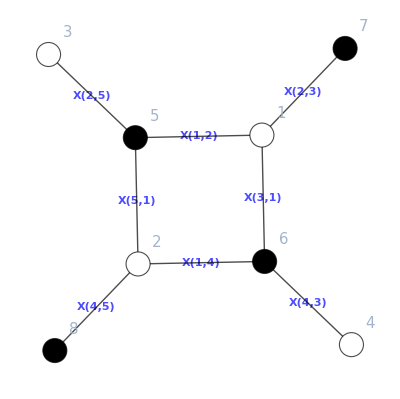

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=1;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix my functional tests*)
```

```mathematica
If[planarityQ[a,b,c,d],
If[totFaces[a,b,c,d]-1=!=polytopeDim[getPmatrix[a,b,c,d]],
(*Print["ii=",ii," : There's a problem with planarityQ! The graph is declared planar even though dim(P)≠F-1"];*)
(*Print[viewGraph[a,b,c,d]];*)
];
,
boundaries=Map[Union@@#&,Gather[Map[Union@@#&,Gather[Map[Union@@#&,Gather[Map[Union@@#&,Gather[Map[List@@#&,Variables[Join[b,c]]],Intersection[#1,#2]=!={}&]],Intersection[#1,#2]=!={}&]],Intersection[#1,#2]=!={}&]],Intersection[#1,#2]=!={}&]];
If[PlanarGraphQ[AdjacencyGraph[getAdjacencyMatrix[a,b,c,d]]]&&Length[boundaries]≤2,
Print["ii=",ii," : There's a problem with planarityQ! The graph is declared nonplanar even though it can be embedded on genus zero and has fewer than 2 boundaries"];
];
If[totFaces[a,b,c,d]-1≥polytopeDim[getPmatrix[a,b,c,d]],
Print["ii=",ii," : There's a problem with planarityQ! The graph is declared nonplanar even though dim(P)≥F-1"];
];
];
```

ii=49 : There's a problem with planarityQ! The graph is declared nonplanar even though it can be embedded on genus zero and has fewer than 2 boundaries

```mathematica
boundaries
```

{{2,3,4}}

```mathematica
polytopeDim[getPmatrix[a,b,c,d]]-totFaces[a,b,c,d]+2
```

4

```mathematica
makeLoopVariablesBasis[a,b,c,d,True]
makeLoopVariablesBasis[a,b,c,d,False]
```

{{(X[3,1] X[5,1])/(X[1,2] X[1,4])},{X[1,2]/(X[2,3] X[2,5]),(X[2,3] X[4,3])/X[3,1],X[1,4]/(X[4,3] X[4,5])}}

{{(X[1,2] X[1,4])/(X[3,1] X[5,1])},{(X[2,5] X[4,5])/X[5,1],(X[2,3] X[4,3])/X[3,1],X[1,4]/(X[4,3] X[4,5])}}